```mathematica
Clear["Global`*"]
```

```mathematica
λ0 = 0.162;
θ0 =0.003737816423136225;
α=0.5029559338070586;
σ=0.34815693559743155;
IndexRefr =Drop[Import[FileNames["*Al2O3.txt",NotebookDirectory[]][[1]],"Table"],2];
δ = Interpolation[IndexRefr[[All,{1,2}]],Method-> "Spline"];
γ = Interpolation[IndexRefr[[All,{1,3}]],Method-> "Spline"];
εε[λ_]:=1-δ[λ]+ⅈ γ[λ]
Rf:=Abs[Cos[#+ArcSin[Cos[#]/√εε[#2]]]/Cos[#-ArcSin[Cos[#]/√εε[#2]]]]^2&
TIS[θ0_,λ_,σ_]:=Rf[θ0,λ](1-Exp[-((4π σ Sin[θ0])/λ)^2])
Rs[θ0_,λ_,σ_]:=Rf[θ0,λ]Exp[-((4π σ Sin[θ0])/λ)^2]
```

```mathematica
k[λ_]:=2π/λ
F[τ_,α_]:=2/(√π)Gamma[α+1/2]/Gamma[α] 1/((1+τ^2)^(α+1/2))
μ0[θ0_,λ_,ξ_]:=ξ 10^3 Sin[θ0]^2/(2λ)
μc[λ_,ξ_]:=ξ 10^3(1-εε[λ])/(2λ)
TISDW[θ0_,λ_,σ_]:=Rf[θ0,λ](2k[λ]σ Sin[θ0])^2
TISNC[θ0_,λ_,σ_]:=Rf[θ0,λ](2k[λ]σ)^2 Sin[θ0]Re[√(εε[λ]-Cos[θ0]^2)]
```

```mathematica
TIS[θ0_,λ_,σ_,ξ_,α_]:=4 √π(k[λ]^2 σ^2 Sin[θ0])/(√(k[λ]ξ 10^3))Rf[θ0,λ](NIntegrate[√(μ0[θ0,λ,ξ]+τ)Abs[(√(μ0[θ0,λ,ξ]+τ)-√(μ0[θ0,λ,ξ]-μc[λ,ξ]+τ))/(√μ0[θ0,λ,ξ]-√(μ0[θ0,λ,ξ]-μc[λ,ξ]))]^2 F[τ,α],{τ,0,ξ 10^3 k[λ]Cos[θ0]/(2π)},MaxRecursion->20]+NIntegrate[√(μ0[θ0,λ,ξ]-τ)Abs[(√(μ0[θ0,λ,ξ]-τ)-√(μ0[θ0,λ,ξ]-μc[λ,ξ]-τ))/(√μ0[θ0,λ,ξ]-√(μ0[θ0,λ,ξ]-μc[λ,ξ]))]^2 F[τ,α],{τ,0,μ0[θ0,λ,ξ]},MaxRecursion->20])
δR[θ0_,λ_,σ_,ξ_,α_]:=4 √π(k[λ]^2 σ^2 Sin[θ0])/(√(k[λ]ξ 10^3))Rf[θ0,λ]Re[2 √(μ0[θ0,λ,ξ]-μc[θ0,λ,ξ])+NIntegrate[(√(μ0[θ0,λ,ξ]+τ)-√(μ0[θ0,λ,ξ]-μc[λ,ξ]+τ))F[τ,α],{τ,0,ξ 10^3 k[λ]Cos[θ0]/(2π)},MaxRecursion->20]+NIntegrate[(√(μ0[θ0,λ,ξ]-τ)-√(μ0[θ0,λ,ξ]-μc[λ,ξ]-τ))F[τ,α],{τ,0,μ0[θ0,λ,ξ]},MaxRecursion->20]]
```

```mathematica
TIS[θ0,λ0,1,#,α]&/@Range[0.5,9.5,1]
```

{0.00212152,0.00399813,0.0054475,0.00671759,0.00787946,0.00896493,0.00999118,0.0109686,0.0119039,0.0128018}

```mathematica
TIS[θcrit[0.834],0.834,1,9.5,α]
TIS[θcrit[0.834],0.834,1]
TISDW[θcrit[0.834],0.834,1]
```

0.012702

0.0181444

0.0188617

```mathematica
θcrit[λ_]:=Abs[1-εε[λ]]^(1/2)
```

```mathematica
θcrit[0.834]
```

0.018543

```mathematica
NSolve[μ0[θcrit[0.834],0.834,x]==25,x]
NSolve[μ0[θ0,λ0,x]==25,x]
```

{{x→121.291}}

{{x→579.764}}

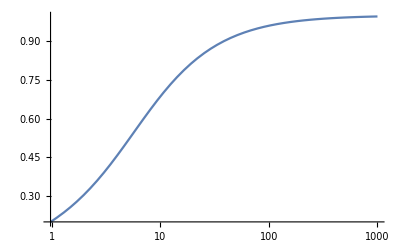

```mathematica
Plot[TIS[θcrit[0.834],0.834,1,x,α]/TISDW[θcrit[0.834],0.834,1],{x,0,10^3},PlotRange->All,ScalingFunctions->{"Log",None}]
```

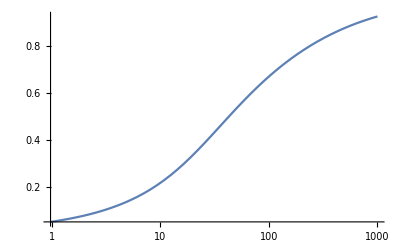

```mathematica
Plot[TIS[θ0,λ0,1,x,α]/TISDW[θ0,λ0,1],{x,0,10^3},PlotRange->All,ScalingFunctions->{"Log",None}]
```

```mathematica
(2k[λ0]Sin[4θ0])^2
```

1.34497

```mathematica
θ=10θ0;
Rf[θ,λ0]TIS[θ,λ0,1,10^7,α]
Rf[θ,λ0]δR[θ,λ0,1,10^7,α]
TISDW[θ,λ0,1]
```

0.0000531057

0.0000531056

0.0000531056

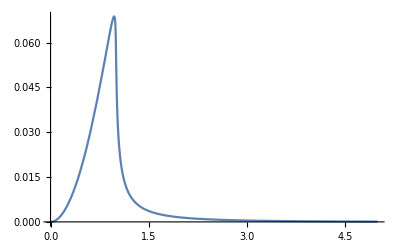

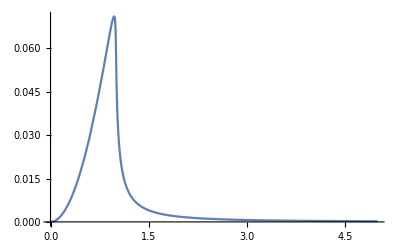

```mathematica
Plot[TIS[x θ0,λ0,1],{x,0,5},PlotRange->All]
Plot[Rf[x θ0,λ0]TIS[x θ0,λ0,1,10^7,α],{x,0,5},PlotRange->All]
```